#### Newton’s interpolation

ω - разделенная разность порядка n
f - значение функции в узлах интерполяции
list - узлы интерполяции

```mathematica
ω[n_,f_,list_]:=Sum[f⟦i⟧/Product[If[k≠ i,list⟦i⟧-list⟦k⟧,1],{k,1,n}],{i,1,n}]
```

```mathematica
interpolant[f_,list_,n_]:=Module[{
a0=1,
a=Table[Product[x - list[[k]], {k, 1, i}], {i, 1, Length@list}]
},
PrependTo[a,a0];
Sum[a⟦k⟧*ω[k,f,list],{k,1,n}]//N//Expand]
```

#### Test 1

```mathematica
list1=RandomInteger[{0,100},100]//DeleteDuplicates//Sort;
f=4#^3+2#^2-6&/@list1;
```

```mathematica
pol=interpolant[f,list1,4]
```

-6.+2. x^2+4. x^3

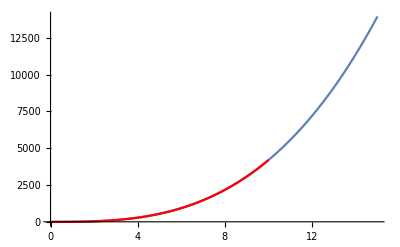

```mathematica
Show[{Plot[4 k^3+2 k^2-6,{k,0,15}],Plot[pol/.x->k,{k,0,10},PlotStyle->Red]}]
```

#### Test 2

```mathematica
list2=RandomReal[{-1,1},30]//DeleteDuplicates//Sort;
```

```mathematica
f2=Exp[#]&/@list1;
```

```mathematica
pol2=interpolant[f2,list1,2]
```

-5.30742+12.6965 x

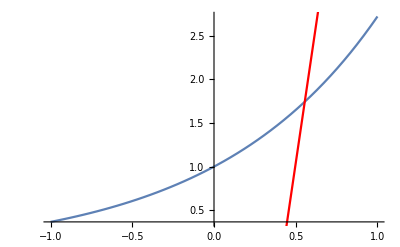

```mathematica
Show[{Plot[Exp[k],{k,-1,1}],Plot[pol2/.x->k,{k,-1,1},PlotStyle->Red]}]
```